```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\maxNt\\scripts\\"]
```

C:\Users\pglpm\repositories\maxNt\scripts

```mathematica
NS["discrepancy_maxent_pop_sample_3rdmoments"]
```

```mathematica
resizewindow
```

```mathematica
popact=Round[Flatten[Import["popact_SANA_bin3.npy","Table"]]];
```

```mathematica
Length[popact]
```

300394

```mathematica
num=159
```

159

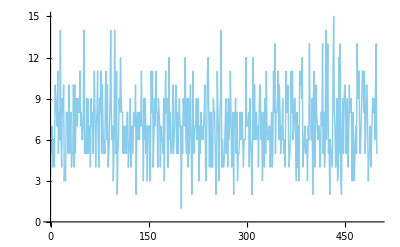

```mathematica
ListPlot[popact[[1;;500]], Joined->True]
```

```mathematica
Mean[popact]/num//N
```

0.0498669

```mathematica
Mean[Binomial[popact,2]/Binomial[num,2]]//N
```

0.00261369

```mathematica
prod[r_]:=prod[r]=(Mean[Binomial[popact,r]/Binomial[num,r]]//N)
```

```mathematica
prod[1]
```

0.0498669

```mathematica
prod[2]
```

0.00261369

```mathematica
prod[3]
```

0.000145633

```mathematica
prod[4]
```

8.76024×10^-6